```mathematica
it = E^((2π* I * D1)/λ) * E^((2π* I * D2)/λ)∫_(d/2 - a/2)^(d/2+a/2) E^((2 π I (w-y1)^2)/(2 * D1 * λ))*E^((2 π I (y1-z)^2)/(2 * D2 * λ))ⅆy1;
ib = E^((2π* I * D1)/λ) * E^((2π* I * D2)/λ) ∫_(-d/2-a/2)^(-d/2+a/2) E^((2 π I (w-y2)^2)/(2 * D1 * λ))*E^((2 π I (y2-z)^2)/(2 * D2 * λ))ⅆy2;
```

```mathematica
(*i = (it + ib)*Conjugate[it+ib];*)
i = (it + ib);
coni = Conjugate[i];
func = i*coni;
```

```mathematica
D1 = 380;
D2 = 700;
λ = .000546;
z = x -6.3;
d = .353;
a = .1;
```

```mathematica
func;
realfunc = 8500*Re[func];
```

```mathematica
SetDirectory["/Users/dluntzma/Desktop/DoubleSlit-ED"];
counts2 = Import["20141122_double_slit_bulb_counts2.csv"];
counts2;
```

```mathematica
fit2 = NonlinearModelFit[counts2,realfunc,{{w,0}}, x];
```

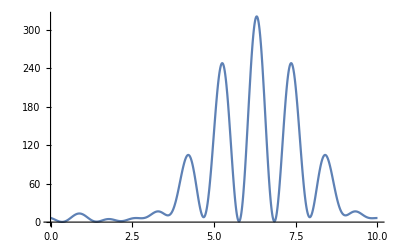

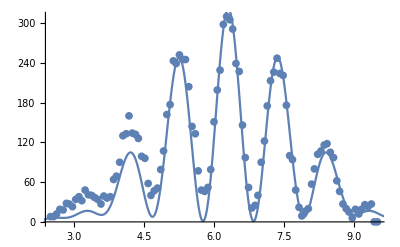

```mathematica
plot2 = Plot[fit2[x], {x, 0, 10},PlotRange->All]
Show[ListPlot[counts2], plot2]
```

```mathematica
ChiSq2=∑_(j=1)^104 ((fit2["FitResiduals"][[j]])/(2(√counts2[[j,2]]-√1.68)))^2
RedChiSq2= ChiSq2/7
```

376.446

53.778